vx→xav+bx xav

vy→yav+by yav+(fyxp vxy)/βy

vz→zav+bz zav+(fzxp vxz)/βz+(fzyp vyz)/βz

vxy→(fyxp vx)/(βx+βy)

vxz→(fzxp vx)/(βx+βz)+(fzyp vxy)/(βx+βz)

vyz→(fzxp vxy)/(βy+βz)+(fyxp vxz)/(βy+βz)+(fzyp vy)/(βy+βz)

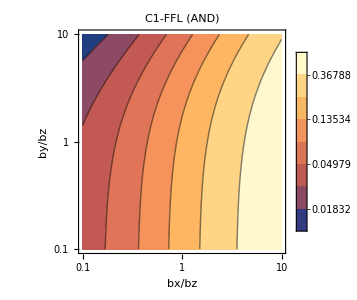
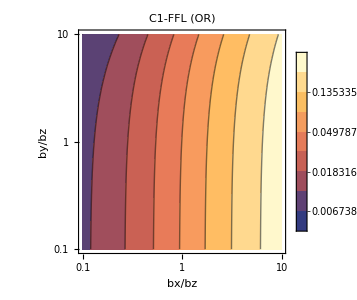
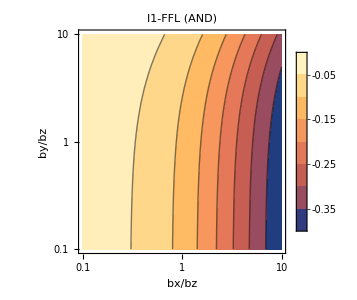
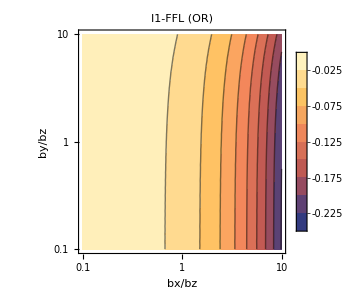
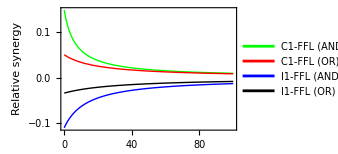
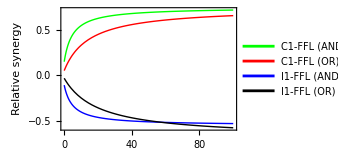
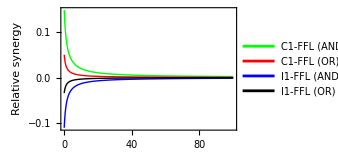
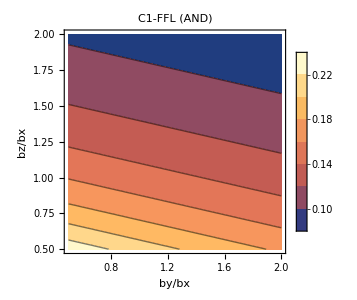
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
(* Lyapunov Solve *)
J=({{-βx, 0, 0}, {fyxp, -βy, 0}, {fzxp, fzyp, -βz}}); (*Jacobian*)
S=({{vx, vxy, vxz}, {vxy, vy, vyz}, {vxz, vyz, vz}}); (*Coiance matrix*)
No=({{2*βx*xav*(1+bx), 0, 0}, {0, 2*βy*yav*(1+by), 0}, {0, 0, 2*βz*zav*(1+bz)}}); (*Noise matrix*)
fac=Factor[J.S+S.Jᵀ+No];
e1=fac[[1,1]];
e2=fac[[1,2]];
e3=fac[[1,3]];
e4=fac[[2,2]];
e5=fac[[2,3]];
e6=fac[[3,3]] ;(*Coupled equation of iances and coiances*)

Expand[Solve[e1==0,vx][[1,1]]]
Expand[Solve[e4==0,vy][[1,1]]]
Expand[Solve[e6==0,vz][[1,1]]]
Expand[Solve[e2==0,vxy][[1,1]]]
Expand[Solve[e3==0,vxz][[1,1]]]
Expand[Solve[e5==0,vyz][[1,1]]]

Quit[];
```